```mathematica
Clear["Global`*"]
```

# Some GW strain calculations

## Strain calculations for exoplanets in the Caltech database. Calculate with eccentricity and distance, etc, the strain at Earth. Frequencies relevant for LISA.

## Notes

20160511 Updated using the new dump of exoplanets from Kepler/NASA.  Also try to include the eccentricity missing and 0 values.
20160609 Look at binning the eccentricity data and make curve that is sqrt(N) (incoherent addition of waves, really RMS) times the collection of modes.
20160627 Kelly suggests uniform binning in log-space.
20160630 Kelly suggests few bins, like 10-ish, and checking the RMS summing with some fake data in the mix.  Especially put the fake data in one of the higher, empty bins.
Really need to break up this notebook into some modules, the Peters&Mathews formulae (as well as others) into a loadable module defining the functions.
20160705 Fix the errors found in the Maggiore power formulae.  See package file GravWavesFunctions.m .  Started this version GWExopEcc2.nb to edit out the chaff and junk.
20171010 Split the file into a package to be loaded with all the cool Peters&Mathews formulae.  Organizing to share with Brittany and Kelly, and to upload to GitHub private repo.

## References

P. Amaro-Seoane et al. “Triplets of supermassive black holes: astrophysics, gravitational waves and detection,” MNRAS 402 2308-2320 (2010);
P. C. Peters and J. Mathews, “Gravitational Radiation from Point Masses in a Keplerian Orbit,” Phys. Rev. 131 (1963) 435-440.
Michele Maggiore, “Gravitational Waves. Volume 1: Theory and Experiments,” Oxford Univ. Press, 2008.

## Directories

```mathematica
(*myDir = "/scratch/gabella/Documents/astro/exop/";*)
(*thisDir = "/home/gabella/Documents/astro/exop/exoplanetsMath/";*)
thisDir = NotebookDirectory[];
csvDir = thisDir <>"dbases/";
pixDir = thisDir <>"pix/";
```

## Eccentric orbits from the exoplanet database.

Some constants.  Work in SI units.

Okay, join the astro / GR world and look at units of length for mass, etc, that is G=c=1 type of unit conversion.

```mathematica
massSun = 1.99 10^30; (*kg *)
massJ = 1.9 10^27; (* kg *)
massE = 5.97 10^24; (* kg *)
massJe = massJ/massE; (* Jupiter mass is 317.9 earth masses *)
massJs = massJ/massSun; (* relative to the sun's mass *)
pc = 30.86 10^15; (* meters, parsec *)
au = 149.6 10^9; (* meters, astron unit *)
cee = 299792458.0; (* meters/s, speed of light *)
secsYear = 365.24*24.0*3600.0; (* s, number of seconds in a year *)
secsDay = 24.0*3600.0; (* s, number of seconds in a day *)
bigG = 6.67384 10^-11; (* SI Gravitational constant, m^3/kg/s *)

rscon = 2*bigG*massSun/cee^2 (* 2955.43 m, solar mass Scharzschild radius *)
lunits =bigG*massSun/cee^2 (* meters per solar mass, units of G=c=1, no factor of 2 as in Schwarzschild radius *)
masscon = lunits; (* m, G Msol/c^2, for 1 solar mass *)

powercon = cee^5/bigG  (* 3.628 10^52 W, c^5/G, W/unit since P is dimensionless in G=c=1 units *)
energycon = cee^4/bigG  (* 1.210 10^44 J/m, c^4/G *)
```

2955.41

1477.7

3.6285×10^52

1.21034×10^44

Some Formulae.  Use Kepler to find the separation in au given the period in days.  The other two are the “normalized” hzero and omega squared divided by c squared from xxxx
and playing with pretty formatting.

```mathematica
Text[Style[ToExpression[
"h_0 = \\frac{r_{s1}\\ r_{s2}}{r\\cdot R}",TeXForm,HoldForm],Large] ]
```

h_0==(r_(s 1) r_(s 2))/(r·R)

r_s1is he Schwarzschild radius for mass 1, etc, r is the distance to earth, R is the separation of the masses 2R.

```mathematica
Text[Style[ToExpression[
"{{\\omega_s^2}\\over{c^2}}  = \\frac{r_{s1} + r_{s2}}{2\\ a^3}",TeXForm,HoldForm],Large] ]
```

ω_s^2/c^2==(r_(s 1)+r_(s 2))/(2 a^3)

the orbital frequency, a is the semi-major axis if elliptical orbits, the radial separation of the masses is 2*R is circular.

```mathematica
sepAU[days_]:=(days/365.24)^(2/3)
(* Test for Null values and return -9999.99 . *)
calchzero[plorbper_, plbmassj_, stmass_, stdist_]:=
plbmassj*massJs*rscon*stmass*rscon/( sepAU[plorbper]*au*stdist*pc )
calcωsq[plorbper_, plbmassj_, stmass_]:=
(plbmassj*massJs+stmass)*rscon/2/(sepAU[plorbper]*au)^3  (* really (ω/c)^2, like k *)
```

## Read the CSV file.

### Run ExoDBase.nb to re-read the cvs file from xxxx.

```mathematica
csvFileName = csvDir<>"exop_20171011_144256.csv"
```

/home/gabella/Documents/astro/exop/exoplanetsMath/dbases/exop_20171011_144256.csv

Find the date-time stamp...lots of StringSplit[]’s.  Will be used in output file names.

```mathematica
dateTimeStamp = Block[{aa,bb,cc},
aa = StringSplit[csvFileName,"/"][[-1]];  (* Filename with stamp is last element. *)
bb = StringSplit[aa,"."][[1]]; (* Drop the .csv extension . *)
cc = StringSplit[bb, "_"]; (* Last two elements are the YYYYMMDD and the HHMMSS strings. *) 
cc[[2]]<>"_"<>cc[[3]]
]
```

20171011_144256

Has first row starting that give the columns and other info.  Column headers in Row number 15, then data as strings??

```mathematica
alldata = Import[csvFileName, "Data"];
```

```mathematica
alldata[[1;;4]] //TableForm(* Look for the row headers. *)
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92
HD 137388 A | b | Radial Velocity | 330. | 0.89 | 0.36 | 0.223 | 38.45 | 0.86 | 2014-05-14 | 26.01

If you use my Mathematica file ExoDBase.nb and/or the https search and NOT the online form, you do not have all the #xxxx header information in the file.  So the rowHeaders is always 1, and rowDataStart is always 2.

```mathematica
rowHeaders=1; rowDataStart=rowHeaders+1;  (* row with the headers, etc . *)
```

From Text file, not CVS, Row 71 has the column headers and Row 72 starts the data.  Cols are
rowid,pl_hostname,pl_letter,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,pl_name,pl_massj
# COLUMN pl_hostname:    Host Name
# COLUMN pl_letter:      Planet Letter
# COLUMN pl_orbper:      Orbital Period [days]
# COLUMN pl_orbsmax:     Orbit Semi-Major Axis [AU]
# COLUMN pl_orbeccen:    Eccentricity
# COLUMN pl_bmassj:      Planet Mass or M*sin(i)[Jupiter mass]
# COLUMN st_dist:        Distance [pc]
# COLUMN st_mass:        Stellar Mass [Solar mass]
# COLUMN pl_name:        Planet Name
# COLUMN pl_massj:       Planet Mass [Jupiter mass]
# COLUMN st_plx:	Star parallax distance [mas], NB: dist in pc is 1000.0/st_plx (in mas)

Find the type of the data fields, when they are actually numbers and not blanks!  Mix of Strings and Reals.

```mathematica
{alldata[[rowHeaders]],
Map[ Head, alldata[[rowDataStart]] ],
alldata[[rowDataStart]]}//TableForm
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
String | String | String | Real | Real | Real | Real | Real | Real | String | Real
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88

```mathematica
Print["Length of the column, the number of columns is ", Length[ alldata[[rowDataStart]] ]  ]
```

Length of the column, the number of columns is 11

Okay it looks like Mathematica treats it as mixed format and guesses pretty well.
Make a dictionary, aka Association in Mathematica, with the header strings to the column numbers / array indices.

```mathematica
cols = <||>;  (* Use an Association as an enum, or Dictionary *)
For[icnt=1, icnt≤Length[ alldata[[rowHeaders]] ], icnt+=1,
AppendTo[cols,alldata[[rowHeaders,icnt]]->icnt]
];
```

```mathematica
Keys[cols]
```

{pl_hostname,pl_letter,pl_discmethod,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx}

```mathematica
{cols["pl_hostname"], cols["pl_orbper"]}
```

{1,4}

## Total power from Peters and Mathews, look at eccentricities

```mathematica
smaf[e_]:=(1+73/24 e^2+37/96 e^4)/((1-e^2)^(7/2)) (* Maggiore's formula Eqn 4.75 page 179. The "small f." *)
```

Graphics suitable for a paper, here, see Peters and Mathews 1963 Fig. 2, “Enhancement Factor.”
http://mathematica.stackexchange.com/questions/47711/preparing-2d-plots-for-publication

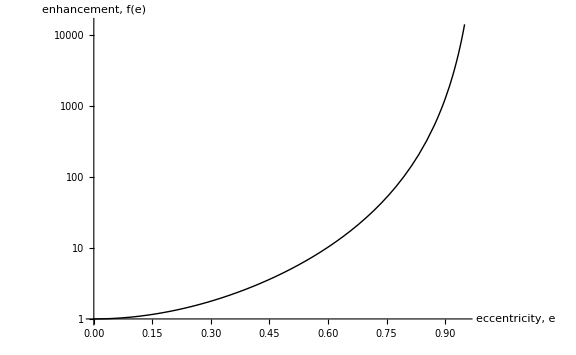

```mathematica
LogPlot[ smaf[e],{e, 0, 0.95},
PlotRange->All,
PlotStyle->{Directive[AbsoluteThickness[1.0], RGBColor[0,0,0] ]},
AxesStyle->Directive[AbsoluteThickness[1.0],12,FontFamily->"Arial"],
AxesLabel->{"eccentricity, e", "enhancement, f(e)", {Left, Bottom}, RotateLabel->True},
ImageSize->8*72

]
```

Create a decent publication worthy plot, I hope.

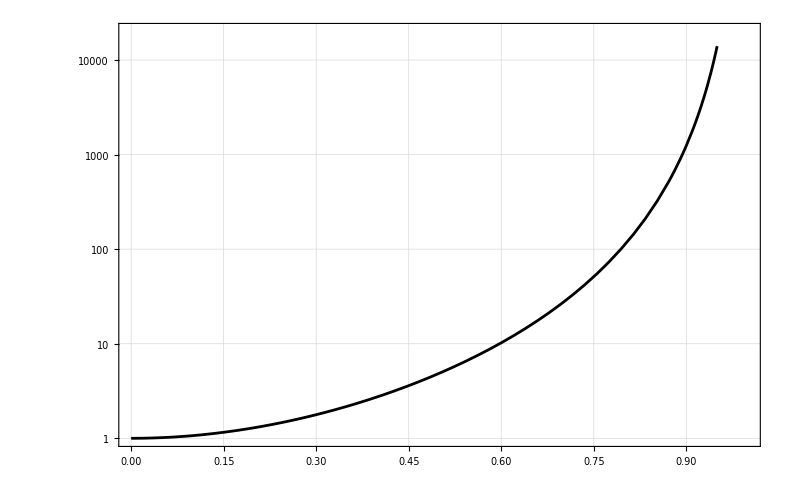
-Graphics-eccentricity, eenhancement, f(e)

```mathematica
If[True,   (* Just want a quick way to turn this off after I have the cool publication plot. *)
Module[{pubPlot,fontPts = 24, tScale=3, tickBig},
pubPlot = Labeled[
LogPlot[ smaf[e],{e, 0, 0.95},
PlotRange->{{0,1},{1,2 10^4}},
Frame->True,
GridLines->Automatic,
BaseStyle->Directive[AbsoluteThickness[1.0], RGBColor[0,0,0], fontPts, FontFamily->"Arial" ],
GridLinesStyle->Directive[AbsoluteThickness[1.0], RGBColor[0,0,0], fontPts, FontFamily->"Arial" ],
PlotStyle->Directive[AbsoluteThickness[2.0], RGBColor[0,0,0], fontPts, FontFamily->"Arial"],
LabelStyle->Directive[AbsoluteThickness[1.0], RGBColor[0,0,0], fontPts, FontFamily->"Arial"],
AxesStyle->Directive[AbsoluteThickness[1.0],RGBColor[0,0,0],fontPts,FontFamily->"Arial"],
FrameStyle->Directive[AbsoluteThickness[1.0],RGBColor[0,0,0],fontPts,FontFamily->"Arial"],
TicksStyle->Directive[AbsoluteThickness[1.0],RGBColor[0,0,0],fontPts,FontFamily->"Arial"],
FrameTicksStyle->Directive[AbsoluteThickness[1.0],fontPts,FontFamily->"Arial"],
LabelStyle->Directive[AbsoluteThickness[1.0],RGBColor[0,0,0],fontPts,FontFamily->"Arial"],
ImageSize->11*72
(*DisplayFunction->$DisplayFunction*)
],

{Style["eccentricity, e", FontFamily->"Arial", FontSize->fontPts], 
Style["enhancement, f(e)", FontFamily->"Arial", FontSize->fontPts]}, 
{Bottom, Left}, RotateLabel->True
];
(*tickBig=Map[MapAt[ tScale # & , #, 3]&, FrameTicks /. AbsoluteOptions[pubPlot, FrameTicks], {2}];*)
Export[pixDir<>"fofe.eps",pubPlot, "EPS" (*, ImageSize->{11,8.5}*72*)];
Show[pubPlot]
],
Null
]
(*Export[myDir<>"g_ecc0p2.png",abar,"PNG", ImageSize->{11,8.5}*72]*)
```

Put some specific eccentricities on the plot, 0.64, 0.511, 0.9332, from Exops “HD 1690”, “GJ 3021”,   “HD 80606”, resp.

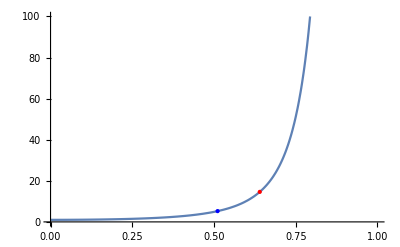

```mathematica
Show[
Plot[smaf[e],{e, 0, 0.95}, PlotRange->{{0,1},{0,100}}],
Graphics[{PointSize[Large],Red,Point[{0.64,smaf[0.64]}]}],
Graphics[{PointSize[Large],Blue,Point[{0.511,smaf[0.511]}]}],
Graphics[{PointSize[Large],Green,Point[{0.9332,smaf[0.9332]}]}]
]
```

```mathematica
{smaf[0.64],smaf[0.511],smaf[0.9332]}
```

{14.6116,5.25036,5092.59}

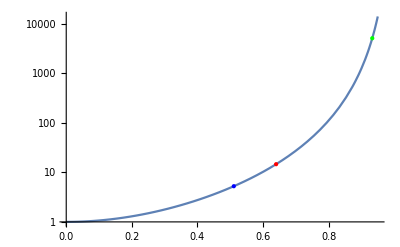

```mathematica
Show[
LogPlot[smaf[e],{e, 0, 0.95}, GridLines->Automatic],
Graphics[{PointSize[Large],Red,Point[{0.64,Log[smaf[0.64]]}]}],
Graphics[{PointSize[Large],Blue,Point[{0.511,Log[smaf[0.511]]}]}],
Graphics[{PointSize[Large],Green,Point[{0.9332,Log[smaf[0.9332]]}]}]
]
```

```mathematica
Solve[smaf[u]==100.0,{u}]  (* Small f = 100 gives and eccentricity of +0.794 , and a negative and many complex roots too. *)
```

{{u→-1.04567-0.199658 ⅈ},{u→-1.04567+0.199658 ⅈ},{u→-0.793955},{u→0.793955},{u→1.04567-0.199658 ⅈ},{u→1.04567+0.199658 ⅈ}}

Formulae for the frequencies of GW from eccentric orbits.
Peters and Mathew 1963, also using Maggiore page 184, and Amaro-Seoane Eqn. (9) plus. See simplified form that Mathematica and Bill found for the g(n,e), called gred(n,e) with fewer Bessel functions.

```mathematica
(* Can Mathematica use underscores yet? Nope, the underscore should be used only to designate the type when dummy function vars. *)
(*aa_bb=23
aa_bb+=2 Error *)
```

```mathematica
??BesselJ
```

BesselJ[n,z] gives the Bessel function of the first kind J_n(z).

Attributes[BesselJ]={Listable,NumericFunction,Protected,ReadProtected}

Maggiore Eqns. 4.94-95, small a_n and small b_n , n≠0 .  Fourier coefficients for x(t) and y(t), all orbital motion in the x-y plane.

```mathematica
jj = BesselJ[#1,#2]&; (* jj = BesselJ will also work fine here. *)
sma[n_,e_, asmaj_]:=asmaj/n(jj[n-1,n*e]-jj[n+1,ne])(* Small a, which n-freq mult/index relative to orbital freq, e-ecc, asmaj-semimajor axis *)
smb[n_,e_, asmaj_]:=asmaj/n(jj[n-1,n*e]-jj[n+1,ne])
```

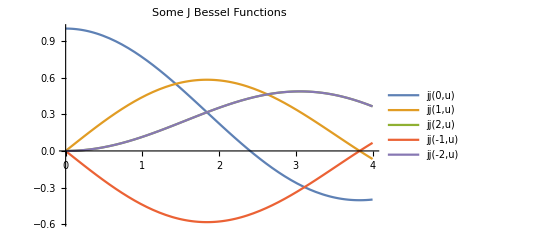

```mathematica
(* check the jj defn *)
Plot[{jj[0,u], jj[1,u], jj[2,u],jj[-1,u], jj[-2,u]},{u, 0, 4},
PlotLabel->"Some J Bessel Functions",
PlotLegends->"Expressions"]
```

Maggiore Eqns. 4.99-101 and his a, b from Eqns. 4.51-52.

```mathematica
bigA[n_,e_, asmaj_]:=asmaj^2/n(jj[n-2,n e]-jj[n+2,n e]-2 e jj[n-1,n e]+2 e jj[n+1,n e] )
bigB[n_,e_, asmaj_]:=(asmaj^2(1-e^2))/n(jj[n+2,n e]-jj[n-2,n e])
bigC[n_,e_, asmaj_]:=(asmaj^2 √(1-e^2))/n(jj[n+2,n e]+jj[n-2,n e]-e jj[n+1,n e]- e jj[n-1,n e] )
gg[n_,e_]:=n^6/(96 asmaj^4)(bigA[n,e,asmaj]^2+bigB[n,e,asmaj]^2+3 bigC[n,e,asmaj]^2-bigA[n,e,asmaj]*bigB[n,e,asmaj])/.asmaj->1  (* The asmaj's cancel out, so set equal to 1.  Same power of asmaj in bigA^2, bigB^2, bigC^2, and bigA*bigB as asmaj^4 *)
```

Check some limits, like e->0.  Then the peak frequency is at 2 ω_0, n=2.

```mathematica
{gg[2,0], gg[1,0.2], gg[1, 0.8]}
```

{1,0.00579633,0.0430687}

Plot Maggiore Fig. 4.8 (maybe), they are normalized to P for e=0 but what a?  Use a=1.  See above does not depend on a, semi-major axis.  He makes a bar chart, see below.

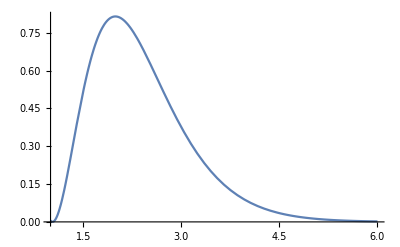

```mathematica
aplot=Plot[gg[n,0.2]/gg[2,0],{n, 1, 6}]
```

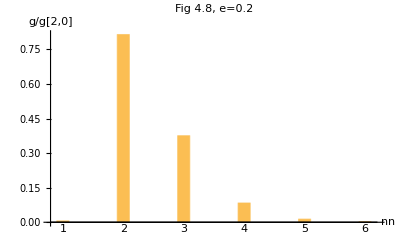

```mathematica
BarChart[ Table[
gg[n,0.2]/gg[2,0],{n, 1, 6}
],
BarSpacing->4, PlotLabel->"Fig 4.8, e=0.2",
AxesLabel->{"n", "g/g[2,0]"},
ChartLabels->{Placed[Table[ii, {ii, 1, 6}],Axis]}]
```

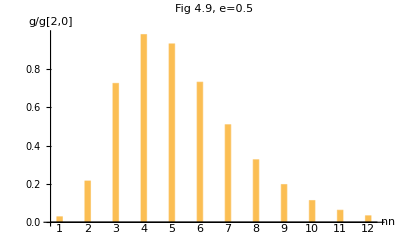

```mathematica
BarChart[ Table[
gg[n,0.5]/gg[2,0],{n, 1, 12}
],
BarSpacing->4,PlotLabel->"Fig 4.9, e=0.5",
AxesLabel->{"n", "g/g[2,0]"},
ChartLabels->{Placed[Table[ii, {ii, 1, 12}],Axis]}]
```

Note below, for eccentricity of 0.7 you shift the peak frequency to 10x orbital (or 5x usual GW), and the GW power is greater than 2x the circular orbit number.

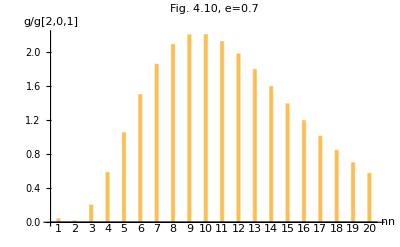

```mathematica
BarChart[ Table[
gg[n,0.7]/gg[2,0],{n, 1, 20}
],
BarSpacing->4, PlotLabel->"Fig. 4.10, e=0.7",
AxesLabel->{"n", "g/g[2,0,1]"},
ChartLabels->{Placed[Table[ii, {ii, 1, 20}],Axis]}]
```

## Now the Caltech Confirmed Expolanets data.

I think the calculation should go, find the orbital frequency f_0 (Hz), from m_1, m_2, and a, then calculate the Power in front of total (Eqn 4.74) or of harmonic (Eqn. 4.107).  Maggiore writes in terms of total mass m=m_1+m_2 and reduced mass μ=(m_1 m_2)/(m_1+m_2) , m_1 and m_2 look easier to me.

```mathematica
freq[m1_, m2_, a_]:=2π √((bigG(m1+m2))/a^3) (* Hz, orbital period, masses and semi-major axis . *)
powerCoeff[m1_,m2_,a_]:=32 bigG^4 (m1^2 m2^2(m1+m2))/(5 cee^5 a^5) (* W, power radiated into n-th mode if times g(n,e), or total if times f(n,e) *)
```

```mathematica
shortList = alldata[[rowDataStart;;rowDataStart+10]];
{alldata[[rowHeaders]]}~Join~shortList//TableForm
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92
HD 137388 A | b | Radial Velocity | 330. | 0.89 | 0.36 | 0.223 | 38.45 | 0.86 | 2014-05-14 | 26.01
GJ 3021 | b | Radial Velocity | 133.71 | 0.49 | 0.511 | 3.37 | 17.62 | 0.9 | 2014-05-14 | 56.76
HD 63454 | b | Radial Velocity | 2.81805 | 0.0368 | 0. | 0.398 | 35.8 | 0.84 | 2015-03-26 | 27.93
HD 212301 | b | Radial Velocity | 2.24572 | 0.036 | 0. | 0.45 | 52.72 | 1.27 | 2014-05-14 | 18.97
CHXR 73 | b | Imaging |  | 210. |  | 12.569 |  | 0.35 | 2014-05-14 | 
CT Cha | b | Imaging |  | 440. |  | 17. | 165. |  | 2014-05-14 | 
HD 196067 | b | Radial Velocity | 3638. | 5.02 | 0.66 | 6.9 | 43.57 | 1.29 | 2014-05-14 | 22.95
HD 68402 | b | Radial Velocity | 1103. | 2.18 | 0.03 | 3.07 | 78. | 1.12 | 2016-11-10 | 12.82
HD 38283 | b | Radial Velocity | 363.2 | 1.02 | 0.41 | 0.34 | 37.78 | 1.08 | 2015-09-10 | 26.47

```mathematica
{cols["pl_orbeccen"], cols["pl_bmassj"]} (* Checking it is defined and agrees with above. *)
```

{6,7}

Just for the shortlist, testing ordering, etc on a few elements not the whole, filtered dataset.

```mathematica
{alldata[[rowHeaders]]}~Join~
Sort[shortList, #1[[cols["pl_orbeccen"] ]]>#2[[cols["pl_orbeccen"] ]]&  ]//TableForm
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
GJ 3021 | b | Radial Velocity | 133.71 | 0.49 | 0.511 | 3.37 | 17.62 | 0.9 | 2014-05-14 | 56.76
HD 137388 A | b | Radial Velocity | 330. | 0.89 | 0.36 | 0.223 | 38.45 | 0.86 | 2014-05-14 | 26.01
HD 212301 | b | Radial Velocity | 2.24572 | 0.036 | 0. | 0.45 | 52.72 | 1.27 | 2014-05-14 | 18.97
HD 63454 | b | Radial Velocity | 2.81805 | 0.0368 | 0. | 0.398 | 35.8 | 0.84 | 2015-03-26 | 27.93
CHXR 73 | b | Imaging |  | 210. |  | 12.569 |  | 0.35 | 2014-05-14 | 
CT Cha | b | Imaging |  | 440. |  | 17. | 165. |  | 2014-05-14 | 
HD 196067 | b | Radial Velocity | 3638. | 5.02 | 0.66 | 6.9 | 43.57 | 1.29 | 2014-05-14 | 22.95
HD 38283 | b | Radial Velocity | 363.2 | 1.02 | 0.41 | 0.34 | 37.78 | 1.08 | 2015-09-10 | 26.47
HD 68402 | b | Radial Velocity | 1103. | 2.18 | 0.03 | 3.07 | 78. | 1.12 | 2016-11-10 | 12.82

Some of the fields are blank, so drop those planets from consideration.

```mathematica
Clear[filterBlanks2]
filterBlanks2[aa_, filterInd_]:=Module[{retList, blankList},
retList={};
blankList={};
For[i=1,i<=Length[aa], i++,
If[ NumberQ[ aa[[i,filterInd]] ], AppendTo[retList, aa[[i]] ], AppendTo[blankList, aa[[i]] ]]
];
{retList, blankList}
]
```

```mathematica
{alldata[[rowHeaders]]}~Join~filterBlanks2[shortList, cols["pl_orbeccen"] ][[1]]//TableForm (* Check that is works, keep the non-blanks in shortlist. *)
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92
HD 137388 A | b | Radial Velocity | 330. | 0.89 | 0.36 | 0.223 | 38.45 | 0.86 | 2014-05-14 | 26.01
GJ 3021 | b | Radial Velocity | 133.71 | 0.49 | 0.511 | 3.37 | 17.62 | 0.9 | 2014-05-14 | 56.76
HD 63454 | b | Radial Velocity | 2.81805 | 0.0368 | 0. | 0.398 | 35.8 | 0.84 | 2015-03-26 | 27.93
HD 212301 | b | Radial Velocity | 2.24572 | 0.036 | 0. | 0.45 | 52.72 | 1.27 | 2014-05-14 | 18.97
HD 196067 | b | Radial Velocity | 3638. | 5.02 | 0.66 | 6.9 | 43.57 | 1.29 | 2014-05-14 | 22.95
HD 68402 | b | Radial Velocity | 1103. | 2.18 | 0.03 | 3.07 | 78. | 1.12 | 2016-11-10 | 12.82
HD 38283 | b | Radial Velocity | 363.2 | 1.02 | 0.41 | 0.34 | 37.78 | 1.08 | 2015-09-10 | 26.47

```mathematica
{alldata[[rowHeaders]]}~Join~filterBlanks2[shortList, cols["pl_orbeccen"] ][[2]]//TableForm (* Show the lines with blank entries. *)
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
CHXR 73 | b | Imaging |  | 210. |  | 12.569 |  | 0.35 | 2014-05-14 | 
CT Cha | b | Imaging |  | 440. |  | 17. | 165. |  | 2014-05-14 |

Filter the blanks in all masses, eccentricity, semimajor axis, and distance.

```mathematica
Print["Length alldata ",Length[alldata] ]
tempdata = alldata;
tempdata= filterBlanks2[tempdata[[rowDataStart;;]], cols["pl_orbeccen"] ][[1]]; Print[ "Number with pl_orbeccen ", Length[tempdata]]
tempdata= filterBlanks2[tempdata, cols["pl_orbper"] ][[1]]; Print[ "Number with pl_orbper ",Length[tempdata] ]
tempdata = filterBlanks2[tempdata, cols["pl_orbsmax"] ][[1]]; Print["Number with pl_orbsmax ",Length[tempdata] ]
tempdata = filterBlanks2[tempdata, cols["pl_bmassj"] ][[1]]; Print["Number with pl_bmassj ",Length[tempdata] ] (* use pl_bmassj not pl_massj *)
tempdata = filterBlanks2[tempdata, cols["st_dist"] ][[1]]; Print["Number with st_dist ",Length[tempdata] ]
tempdata = filterBlanks2[tempdata, cols["st_mass"] ][[1]]; Print["Number with st_mass ",Length[tempdata] ]
```

Length alldata 3530

Number with pl_orbeccen 1112

Number with pl_orbper 1112

Number with pl_orbsmax 1049

Number with pl_bmassj 989

Number with st_dist 889

Number with st_mass 858

```mathematica
fdata = tempdata; (* The filtered data. *)
Length[fdata]
```

858

```mathematica
{alldata[[rowHeaders]]}~Join~fdata[[10;;14]]//TableForm
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 131664 | b | Radial Velocity | 1951. | 3.17 | 0.638 | 18.15 | 57.21 | 1.1 | 2014-05-14 | 17.48
HD 108341 | b | Radial Velocity | 1129. | 2. | 0.85 | 3.5 | 49.4 | 0.84 | 2015-01-08 | 20.23
HD 222076 | b | Radial Velocity | 871. | 1.83 | 0.08 | 1.56 | 83.5 | 1.07 | 2016-12-01 | 
WASP-91 | b | Transit | 2.79858 | 0.037 | 0. | 1.34 | 150.72 | 0.84 | 2017-08-17 | 6.63
HD 216437 | b | Radial Velocity | 1256. | 2.32 | 0.29 | 1.82 | 26.52 | 1.15 | 2015-04-24 | 37.71

```mathematica
Print["Fraction of confirmed exoplanets we can use in this calculation ",N[Length[fdata]/Length[alldata],3 ], " ." ]
```

Fraction of confirmed exoplanets we can use in this calculation 0.243 .

Only 24% have all the data fields I am about to use.  Maybe there is some minimal set, the fields are not all independent and Kepler’s laws might be used to infer the missing data.  For now use the “fdata.”  
[Seem to be repeating the formulae from above with new names, and asmaj instead of a. ? ]

```mathematica
pwrTot[m1_,m2_,asmaj_]:=32 bigG^4 ((m1 m2)^2(m1+m2))/(5 cee^5 asmaj^5)  (* W, Lead coefficient in eqn. 4.74 for total power radiated from orbiting masses in an eccentric orbit. *)
pwrSubN[m1_,m2_,asmaj_]:=pwrTot[m1,m2,asmaj]  (* Lead coefficient for eqn. 4.107, power in nth harmonic. *)
```

## Removed three gg[] comparison section, to file ThreeGsGWEccen.nb . Oops need the definitions of ggPM and ggAS. gg given above is Maggiore’s definition.

Peters and Mathews

```mathematica
ggPM[n_,e_]:= n^4/32( (jj[n-2,n e]-2 e jj[n-1,n e]+2/n jj[n, n e]+2 e jj[n+1, n e]-jj[n+2, n e])^2+
(1-e^2)(jj[n-2,n e]-2 jj[n, n e]+jj[n+2, n e])^2 +4/(3 n^2)jj[n, n e]^2 )
```

Amaro-Seoane et al.

```mathematica
bigAAS[n_,e_]:=jj[n-2,n e]-2 jj[n, n e]+jj[n+2,n e]
bigBAS[n_,e_]:=jj[n-2,n e]-2 e jj[n-1,n e]+2/n jj[n,n e]+2 e jj[n+1,n e]-jj[n+2,n e]
ggAS[n_, e_]:=n^4/32(bigBAS[n,e]^2 + (1-e^2)bigAAS[n,e]^2+4/(3 n^2)jj[n,n e]^2)
```

## gred simplification to all these little g(n,e)’s .

Below found from Mathematica simplify of the full Bessel function expression---thank you, Mathematica.  Obviously NOT a singularity at e=0, which is less obvious from gred vs ggPM, etc.

```mathematica
gred[n_,e_]:=n^2/(6 e^4)(
3 e^2 (-1+e^2) (-1+(-1+e^2) n^2) BesselJ[-1+n,e n]^2-3 e (-1+e^2) (-2+n (-2 (2+n)+e^2 (3+2 n))) BesselJ[-1+n,e n] BesselJ[n,e n]+(-3 e^6 n^2+6 (1+n)^2-3 e^2 (1+n) (2+5 n)+e^4 (1+3 n (3+4 n))) BesselJ[n,e n]^2   )
```

```mathematica
nlist = Table[ii, {ii, 1,6}];{Map[ gred[#,0.2]&, nlist ],Map[ gg[#,0.2]&, nlist ],Map[ ggAS[#,0.2]&, nlist ],
Map[ gg[#,0.2]&, nlist ]}//TableForm
```

0.00579633 | 0.814184 | 0.37536 | 0.0835568 | 0.0136303 | 0.00186696
0.00579633 | 0.814184 | 0.37536 | 0.0835568 | 0.0136303 | 0.00186696
0.00579633 | 0.814184 | 0.37536 | 0.0835568 | 0.0136303 | 0.00186696
0.00579633 | 0.814184 | 0.37536 | 0.0835568 | 0.0136303 | 0.00186696

```mathematica
nlist = Table[ii, {ii, 2,20, 4}];{Map[ gred[#,0.9]&, nlist ],Map[ ggPM[#,0.9]&, nlist ],Map[ ggAS[#,0.9]&, nlist ],
Map[ gg[#,0.9]&, nlist ]}//TableForm
```

0.0517622 | 0.0993781 | 0.716376 | 2.12475 | 4.18257
0.0517622 | 0.0993781 | 0.716376 | 2.12475 | 4.18257
0.0517622 | 0.0993781 | 0.716376 | 2.12475 | 4.18257
0.0517622 | 0.0993781 | 0.716376 | 2.12475 | 4.18257

```mathematica
nlist = Table[ii, {ii, 1,4}];{Map[ gred[#,0.001]&, nlist ],Map[ ggPM[#,0.001]&, nlist ],Map[ ggAS[#,0.001]&, nlist ],
Map[ gg[#,0.001]&, nlist ]}//TableForm
```

1.51054×10^-7 | 0.999995 | 0.0000113906 | 6.39997×10^-11
1.51042×10^-7 | 0.999995 | 0.0000113906 | 6.39997×10^-11
1.51042×10^-7 | 0.999995 | 0.0000113906 | 6.39997×10^-11

Some absolute differences with gg, e = 0.9 .

```mathematica
nlist = Table[ii, {ii, 2,20, 4}];
ecc = 0.9;
{Map[( gred[#,ecc]-gg[#,ecc])&, nlist ],
Map[ (ggPM[#,ecc]-gg[#,ecc])&, nlist ],
Map[ (ggAS[#,ecc]-gg[#,ecc])&, nlist ]}//TableForm
```

-1.80411×10^-16 | 5.8703×10^-15 | 4.61853×10^-14 | -2.02505×10^-13 | 9.81437×10^-13
2.77556×10^-17 | -5.55112×10^-17 | 1.11022×10^-16 | 1.02141×10^-13 | -2.56684×10^-13
2.77556×10^-17 | -5.55112×10^-17 | 1.11022×10^-16 | 1.02141×10^-13 | -2.56684×10^-13

```mathematica
nlist = Table[ii, {ii, 1, 4}];
ecc = 0.001;
{Map[( gred[#,ecc]-gg[#,ecc])&, nlist ],
Map[ (ggPM[#,ecc]-gg[#,ecc])&, nlist ],
Map[ (ggAS[#,ecc]-gg[#,ecc])&, nlist ]}//TableForm
```

1.26972×10^-11 | -1.88738×10^-15 | -1.52466×10^-20 | -2.58494×10^-26
0. | 0. | 1.69407×10^-21 | 1.29247×10^-26
0. | 0. | 1.69407×10^-21 | 1.29247×10^-26

## Estimate max frequency harmonic n given the eccentricity e. Use Peters and Mathews g(n,e) as the industry standard.

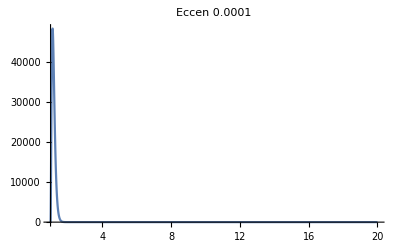
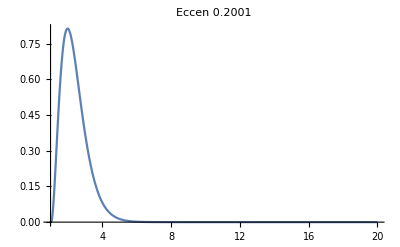
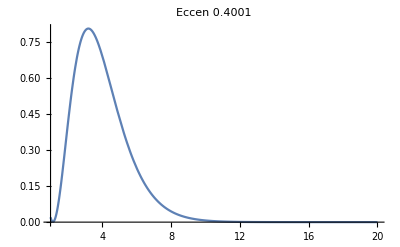
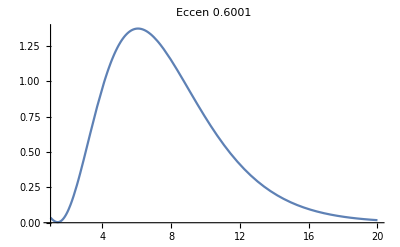

```mathematica
Table[
Plot[ggPM[n,e]/ggPM[2,0],{n, 1, 20}, PlotRange->All,PlotLabel->"Eccen "<>ToString[e]],{e, 0.0001, 0.8, 0.2}
]
```

Numerically solve for the n-star on the falling tail of the above functions that is at some small-ish absolute value, less than the peak obviously.
Looking for ways to search for the second, tail decrease below some threshold.
Below shows you have to worry about the rising edge too.

```mathematica
(* NSolve[ggPM[nn,0.7]==0.05&&nn>2,nn, Reals] *)
aa=Table[{nn,ggPM[nn,0.7], ggPM[nn,0.7]<0.05},{nn,1,40}]
(* So, 30, 0.05498 and then 31, 0.04238, puts 0.05 around n = 30+(31-30)/(0.0428-0.05498)*(0.05-0.05498)   *)
```

{{1,0.0413106,True},{2,0.0167665,True},{3,0.203845,False},{4,0.587497,False},{5,1.05607,False},{6,1.5034,False},{7,1.86036,False},{8,2.09591,False},{9,2.20752,False},{10,2.21008,False},{11,2.12669,False},{12,1.98238,False},{13,1.80025,False},{14,1.59957,False},{15,1.39521,False},{16,1.19775,False},{17,1.01415,False},{18,0.848358,False},{19,0.702122,False},{20,0.575587,False},{21,0.467848,False},{22,0.377364,False},{23,0.302269,False},{24,0.240588,False},{25,0.190388,False},{26,0.149865,False},{27,0.117391,False},{28,0.0915389,False},{29,0.071082,False},{30,0.0549824,False},{31,0.0423754,True},{32,0.0325487,True},{33,0.0249217,True},{34,0.0190253,True},{35,0.0144835,True},{36,0.0109969,True},{37,0.00832899,True},{38,0.00629355,True},{39,0.004745,True},{40,0.00356996,True}}

```mathematica
nstar=30+(31-30)/(aa[[31,2]]-aa[[30,2]])*(0.05-aa[[30,2]]) (* linear interpolation to find the 0.05 point*)
```

30.3952

Check the Floor and Ceiling of the nstar.

```mathematica
{ggPM[Floor[nstar],0.7],ggPM[nstar,0.7],ggPM[Ceiling[nstar],0.7]}
```

{0.0549824,0.0496254,0.0423754}

```mathematica
(* A local equation solver, but NSolve is a global one.
Agrees with above manual linear interpolation from the generated table. *)
FindRoot[ggPM[nn,0.7]==0.05,{nn,20}]
```

{nn→30.3663}

More elaborate search for the second root, where the curve is coming down toward 0.

```mathematica
Clear[findSecondRoot];
findSecondRoot[ee_, lim_]:=Module[{alist,nmax=200,iloop=True, ifirstRoot=False, ii, prev},
alist=Table[{ii,ggPM[ii,ee]-lim>0 },{ii, 1, nmax}];  (* Check for neg, then pos, then neg, there is second root. *)
ii=1;
prev=alist[[ii,2]];
While[iloop,
If[ Xor[prev,alist[[ii,2]]],
If[ifirstRoot==False,ifirstRoot=True, iloop=False ], ];(* True when goes from neg to pos in above ggPM-lim. *)
prev = alist[[ii,2]];
ii++;
];
(* Now ii is near second root. *)
FindRoot[ggPM[nn,ee]-lim==0,{nn,ii}]
]
```

```mathematica
{ggPM[2.31616,0.7], ggPM[30.3663, 0.7]}
```

{0.0499993,0.0499998}

```mathematica
findSecondRoot[0.7,0.05]
```

{nn→30.3663}

```mathematica
ee=Range[0.1,0.9,0.05];
maxNdata=Table[
{ee[[i]],findSecondRoot[ee[[i]], 0.05]},{i,1,Length[ee]}
]
```

{{0.1,{nn→3.28484}},{0.15,{nn→3.75374}},{0.2,{nn→4.29642}},{0.25,{nn→4.9412}},{0.3,{nn→5.72119}},{0.35,{nn→6.67979}},{0.4,{nn→7.87705}},{0.45,{nn→9.39924}},{0.5,{nn→11.3747}},{0.55,{nn→14.0019}},{0.6,{nn→17.6017}},{0.65,{nn→22.7222}},{0.7,{nn→30.3663}},{0.75,{nn→42.5429}},{0.8,{nn→63.8058}},{0.85,{nn→106.539}},{0.9,{nn→4.76851}}}

The trouble above is that e=0.9 has a second root at nn=4.8 and the third root is really of interest to us.

```mathematica
{maxNdata[[1,1]], maxNdata[[1,2, 1,2]]}  (* Second 1,2,1,2 gets at the number in n->3.284... *)
```

{0.1,3.28484}

```mathematica
maxNdata2 = Table[
{maxNdata[[i,1]],maxNdata[[i,2,1,2]]},{i, 1, Length[maxNdata]}
](* eccentricity 0.9 is trouble because of the rise and fall at the start.  *)
```

{{0.1,3.28484},{0.15,3.75374},{0.2,4.29642},{0.25,4.9412},{0.3,5.72119},{0.35,6.67979},{0.4,7.87705},{0.45,9.39924},{0.5,11.3747},{0.55,14.0019},{0.6,17.6017},{0.65,22.7222},{0.7,30.3663},{0.75,42.5429},{0.8,63.8058},{0.85,106.539},{0.9,4.76851}}

Fix the high eccentricity point by hand.

```mathematica
FindRoot[ggPM[nn,0.9]-0.05==0,{nn,190}]
```

{nn→216.182}

```mathematica
maxNdata2[[17]]
```

{0.9,4.76851}

```mathematica
maxNdata3=ReplacePart[maxNdata2,17->{0.9,216.182}]
```

{{0.1,3.28484},{0.15,3.75374},{0.2,4.29642},{0.25,4.9412},{0.3,5.72119},{0.35,6.67979},{0.4,7.87705},{0.45,9.39924},{0.5,11.3747},{0.55,14.0019},{0.6,17.6017},{0.65,22.7222},{0.7,30.3663},{0.75,42.5429},{0.8,63.8058},{0.85,106.539},{0.9,216.182}}

Below is the point of this section, to find a fast way to estimate a large n-star that is still relevant to consider for GW power radiated, i.e. 1/20 (=0.05) of the circular orbit n=2 power.

```mathematica
(*fitEcc2N = Fit[maxNdata3, {1,x,x^2, x^3},x]*) (* This does not work well at all. *)
```

```mathematica
fitEcc2N2 = NonlinearModelFit[maxNdata3,(a+b x +c x^2)Exp[d x],{a,b,c,d},x]
```

FittedModel[ⅇ^(9.52122 x) (0.589993-1.41301 x+0.892102 x^2)]

```mathematica
ecc2n=Normal[fitEcc2N2]
```

ⅇ^(9.52122 x) (0.589993-1.41301 x+0.892102 x^2)

```mathematica
ecc2n/.x->0.4
```

7.55246

```mathematica
{fitEcc2N2[0.0],fitEcc2N2[0.4],fitEcc2N2[0.9], fitEcc2N2[0.99]}
```

{0.589993,7.55246,215.34,812.225}

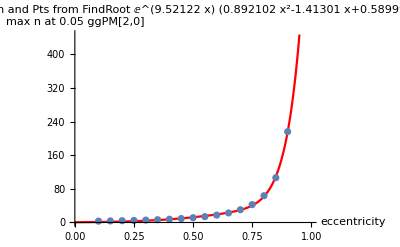

```mathematica
aeccPlot=Show[{
Plot[fitEcc2N2[x],{x, 0, 0.95}, PlotRange->{{0,1},All},PlotStyle->{RGBColor[1,0,0]},
PlotLabel->"Fit Fcn and Pts from FindRoot\n"ecc2n, AxesLabel->{"eccentricity","max n at 0.05 ggPM[2,0]"}],
ListPlot[ maxNdata3, PlotRange->{{0,1},All}, PlotLabel->"From FindRoot"]
(*Plot[fitEcc2N,{x,0,0.9}]*)
}]
```

```mathematica
(*Export[myDir<>"nMaxFromEcc.png",aeccPlot,"PNG", ImageSize→{11,8.5}*72]*)
```

The trouble with ecc = 0.9, there are extra roots at the front, so the high-n n-star is the third root.
Below plots the 0.05 threshold and the ggPM[n,0.9] .

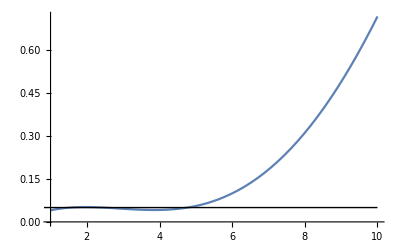

```mathematica
Show[{
Plot[ggPM[nn,0.9],{nn,1,10}],
Graphics[Line[{{0, 0.05},{10,0.05}}]  ]
}]
```

## Amaro-Seoane et al. Eqn. (9) and (10) toward Strain Sensitivity hf.

h_n Eqn. (9).

```mathematica
Clear[chirpM,redM, totM, fr, hh]
chirpM[m1_,m2_]:=(m1 m2)^(3/5)/(m1+m2)^(1/5)
redM[m1_,m2_]:=(m1 m2)/(m1+m2)
totM[m1_,m2_]:=m1+m2
fr[m1_,m2_,a_]:=1/(2 π)√((bigG(m1+m2))/a^3)
hh [n_,e_,m1_,m2_,a_, dL_]:= bigG^(5/3)/cee^4 2 √(32/5)chirpM[m1,m2]^(5/3)/(n dL)(2π fr[m1,m2,a])^(2/3) √ggAS[n,e]  (* Subscript[d, L] is luminosity distance d=Subscript[d, L]/(1+z), z=0 for us, Subscript[f, r] is orbital freq *)
```

```mathematica
{alldata[[rowHeaders]]}~Join~shortList//TableForm
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92
HD 137388 A | b | Radial Velocity | 330. | 0.89 | 0.36 | 0.223 | 38.45 | 0.86 | 2014-05-14 | 26.01
GJ 3021 | b | Radial Velocity | 133.71 | 0.49 | 0.511 | 3.37 | 17.62 | 0.9 | 2014-05-14 | 56.76
HD 63454 | b | Radial Velocity | 2.81805 | 0.0368 | 0. | 0.398 | 35.8 | 0.84 | 2015-03-26 | 27.93
HD 212301 | b | Radial Velocity | 2.24572 | 0.036 | 0. | 0.45 | 52.72 | 1.27 | 2014-05-14 | 18.97
CHXR 73 | b | Imaging |  | 210. |  | 12.569 |  | 0.35 | 2014-05-14 | 
CT Cha | b | Imaging |  | 440. |  | 17. | 165. |  | 2014-05-14 | 
HD 196067 | b | Radial Velocity | 3638. | 5.02 | 0.66 | 6.9 | 43.57 | 1.29 | 2014-05-14 | 22.95
HD 68402 | b | Radial Velocity | 1103. | 2.18 | 0.03 | 3.07 | 78. | 1.12 | 2016-11-10 | 12.82
HD 38283 | b | Radial Velocity | 363.2 | 1.02 | 0.41 | 0.34 | 37.78 | 1.08 | 2015-09-10 | 26.47

```mathematica
Clear[aNmax];
aNmax[ecc_]:=If[ecc==0, 2, Floor[fitEcc2N2[ecc]+1]]
Clear[aNmin];
aNmin[ecc_]:=If[ecc==0,1, 1](* A little silly, but played with n=2 for e=0 since the only one but want a range, so 1 to 2 for e=0. *)
```

Test the above formulae on this short table.

Create string names without the underscore and with an "a" in front!  Later make them an expression (symbol?) so they can hold the data.

```mathematica
colNamesStr=Module[{aa, bb, myname},
aa=alldata[[rowHeaders]];
bb={};
For[ii=1, ii≤Length[aa], ii++,
myname="a"<>StringReplace[aa[[ii]],"_"->""];
AppendTo[bb, myname  ]
];
bb
]
```

{aplhostname,aplletter,apldiscmethod,aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx}

Want to use the names aplhostname, aplletter, astdist, ..., to be the lists/arrays with the data from the CSV file.

```mathematica
Remove[colNames, aplhostname,aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx]
bdata = shortList[[1;;5]]
(*colNames=Transpose[ bdata ];*)(* Headers not in shortList, used alldata[[rowHeaders]] *)
colNames = alldata[[rowHeaders]];
{aplhostname,aplletter, apldiscmethod, aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx}=Transpose[ bdata ];
colNames[[cols["pl_hostname"]]]
colNames[[cols["pl_bmassj"]]]
aplorbper
astdist
```

{{HD 142022 A,b,Radial Velocity,1928.,3.03,0.53,5.1,35.87,0.99,2014-05-14,27.88},{HD 39091,b,Radial Velocity,2151.,3.38,0.6405,10.27,18.21,1.1,2014-07-23,54.92},{HD 137388 A,b,Radial Velocity,330.,0.89,0.36,0.223,38.45,0.86,2014-05-14,26.01},{GJ 3021,b,Radial Velocity,133.71,0.49,0.511,3.37,17.62,0.9,2014-05-14,56.76},{HD 63454,b,Radial Velocity,2.81805,0.0368,0.,0.398,35.8,0.84,2015-03-26,27.93}}

pl_hostname

pl_bmassj

{1928.,2151.,330.,133.71,2.81805}

{35.87,18.21,38.45,17.62,35.8}

```mathematica
row
```

{{HD 39091,b,Radial Velocity,2151.,3.38,0.6405,10.27,18.21,1.1,2014-07-23,54.92},{HD 137388 A,b,Radial Velocity,330.,0.89,0.36,0.223,38.45,0.86,2014-05-14,26.01},{GJ 3021,b,Radial Velocity,133.71,0.49,0.511,3.37,17.62,0.9,2014-05-14,56.76},{HD 63454,b,Radial Velocity,2.81805,0.0368,0.,0.398,35.8,0.84,2015-03-26,27.93}}

Set::shape: Lists {aplhostname,aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx} and {{HD 39091,HD 137388 A,GJ 3021,HD 63454},{b,b,b,b},{Radial Velocity,Radial Velocity,Radial Velocity,Radial Velocity},«5»,{1.1,0.86,0.9,0.84},{2014-07-23,2014-05-14,2014-05-14,2015-03-26},{54.92,26.01,56.76,27.93}} are not the same shape.

{HD 39091,HD 137388 A,GJ 3021,HD 63454}

{10.27,0.223,3.37,0.398}

aplorbper

astdist

```mathematica
(* Create a list of eccen, {{freq(Hz)_1, h_1},{freq_2, h_2}....}  *)
 atab=Table[
{bdata[[nn,cols["pl_orbeccen"] ]], 
Table[
Module[{afr},
afr = fr[aplbmassj[[nn]]*massJs*massSun, astmass[[nn]]*massSun, aplorbsmax[[nn]]*au];
{pp*afr, hh [pp,aplorbeccen[[nn]],aplbmassj[[nn]]*massJs*massSun,astmass[[nn]]*massSun,aplorbsmax[[nn]]*au, astdist[[nn]]*pc]}
], {pp,1,Max[ {aNmax[ aplorbeccen[[nn]] ], 3}] }
]},
{nn, 1, Length[bdata]}
];
atab//TableForm
```

Part::partd: Part specification aplorbeccen⟦1⟧ is longer than depth of object.

Table::iterb: Iterator {pp,1,Max[3,If[aplorbeccen⟦1⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦1⟧]+1]]]} does not have appropriate bounds.

Part::partd: Part specification aplorbeccen⟦2⟧ is longer than depth of object.

Table::iterb: Iterator {pp,1,Max[3,If[aplorbeccen⟦2⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦2⟧]+1]]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partd: Part specification aplorbeccen⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

0.53 | Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[aplorbeccen⟦1⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦1⟧]+1]]]}]
0.6405 | Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[aplorbeccen⟦2⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦2⟧]+1]]]}]
0.36 | Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[aplorbeccen⟦3⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦3⟧]+1]]]}]
0.511 | Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[aplorbeccen⟦4⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦4⟧]+1]]]}]

```mathematica
Remove[colNames,aplhostname,aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx]
 bdata = fdata6; (* Data filtered to have non-null entries in the fields we want. *)
{aplhostname,aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx}=Transpose[ bdata ];
```

Set::shape: Lists {aplhostname,aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx} and {{HD 142022 A,HD 39091,HD 137388 A,GJ 3021,HD 63454,HD 212301,HD 196067,HD 68402,HD 38283,HD 131664,HD 108341,«30»,HD 10180,HD 10180,HD 10180,HD 10180,HD 10180,HD 10180,HD 142415,HD 23127,HD 40307,«764»},«10»} are not the same shape.

```mathematica
(* Create a list of eccen, {{freq(Hz)_1, h_1},{freq_2, h_2}....}  *)
 atab=Table[
{bdata[[nn,cols["pl_orbeccen"] ]], 
Table[
Module[{afr},
afr = fr[aplbmassj[[nn]]*massJs*massSun, astmass[[nn]]*massSun, aplorbsmax[[nn]]*au];
{pp*afr, hh [pp,aplorbeccen[[nn]],aplbmassj[[nn]]*massJs*massSun,astmass[[nn]]*massSun,aplorbsmax[[nn]]*au, astdist[[nn]]*pc]}
], {pp,1,Max[ {aNmax[ aplorbeccen[[nn]] ], 3}] }
]},
{nn, 1, Length[bdata]}
];
atab[[12;;16]]//TableForm
```

Part::partd: Part specification aplorbeccen⟦1⟧ is longer than depth of object.

Table::iterb: Iterator {pp,1,Max[3,If[aplorbeccen⟦1⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦1⟧]+1]]]} does not have appropriate bounds.

Part::partd: Part specification aplorbeccen⟦2⟧ is longer than depth of object.

Table::iterb: Iterator {pp,1,Max[3,If[aplorbeccen⟦2⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦2⟧]+1]]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partd: Part specification aplorbeccen⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

0.08 | Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[aplorbeccen⟦12⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦12⟧]+1]]]}]
0.29 | Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[aplorbeccen⟦13⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦13⟧]+1]]]}]
0.54 | Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[aplorbeccen⟦14⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦14⟧]+1]]]}]
0.18 | Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[aplorbeccen⟦15⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦15⟧]+1]]]}]
0.7 | Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[aplorbeccen⟦16⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦16⟧]+1]]]}]

```mathematica
{atab[[1]], atab[[3]]}
```

{{0.53,Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[aplorbeccen⟦1⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦1⟧]+1]]]}]},{0.36,Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[aplorbeccen⟦3⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦3⟧]+1]]]}]}}

```mathematica
{atab[[1,2]], atab[[1,2, 1, 1]], atab[[1,2, 2, 1]],Length[  atab[[1,2]]  ]}
```

{Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[aplorbeccen⟦1⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦1⟧]+1]]]}],{afr},pp,2}

Make lists to plot freq vs eccen.

```mathematica
freqVecc = Table[
Table[
{atab[[ii,1]],atab[[ii,2,kk, 1]]},{kk, 1, Length[ atab[[ii,2]] ]}
],
{ii, 1, Length[atab]}
];
freqVecc[[1;;3]]
```

{{{0.53,{afr}},{0.53,pp}},{{0.6405,{afr}},{0.6405,pp}},{{0.36,{afr}},{0.36,pp}}}

```mathematica
alogplot=ListLogPlot[freqVecc, 
PlotLabel->"Freq(Hz) vs Eccentricity",
AxesLabel->{"eccentricity, e", "GW frequency, Hz"}]
```

-Graphics-

```mathematica
mylen=Length[atab]
```

814

```mathematica
fileString = myDir<>"freqVecc"<>ToString[mylen]<>"exop.png" ;Export[fileString, alogplot, "PNG", ImageSize→{11,8.5}*72]
```

Now for the hf calculation following Amaro-Seoane et al.  Already have h with correct units (unitless) above.  Note the G^(5/3)/c^4~6.3×10^-55.  But for strain sensitivity, do the AS eqn. (10) enhancement,
 hobs,n = h_n  √(T f_(r n)) , where T is max(T_orb, T_obs), so that T f_(f n)= 1 or N_orbs, the latter if observed for many orbital periods.  So their formula is like a sqrt(N) incoherent addition of wave amplitudes.
 Used 3 years and 10 years for LISA observing T_obs...in previous exoplanet work (Hot Jupiters).

```mathematica
rootNfcn := Sqrt[ Max[ #1, #2]*#3/#1 ]&; (* #1 is Subscript[t, orb], #2 is Subscript[t, obs], same units!, #3 is the n of the harmonic, 2 for circular *)
```

```mathematica
rootNfcn[14002.,3*365.24, {1,2,3}]
```

{1.,1.41421,1.73205}

```mathematica
rootTab=Table[
Table[
{fdata6[[ii,cols["pl_orbper"]]],rootNfcn[fdata6[[ii,cols["pl_orbper"]]]*secsDay, 3*secsYear, kk]} ,{kk, 1, Length[ atab[[ii,2]] ]}
],
{ii, 1, Length[atab]}
];
rootTab[[12;;14]]
```

{{{871.,1.12161},{871.,1.58619}},{{1256.,1.},{1256.,1.41421}},{{1290.,1.},{1290.,1.41421}}}

First just points and then
 “bin” the frequency.  Use AS et al.’s hobs,n and then multiply by Sqrt[T_obs].

```mathematica
{Length[atab], Length[fdata6]}  (* Should be in the same order too.  CHECK THIS! *)
```

{814,814}

```mathematica
{atab[[2,2,{1,2,3}, 1]], atab[[2,2]], Length[atab[[2,2]] ], fdata6[[2,cols["pl_orbper"]]],
rootNfcn[fdata6[[2,cols["pl_orbper"]]]*secsDay, 3*secsYear, {1,2,3}]}
```

Part::partw: Part {1,2,3} of Table[Module[{afr},afr=fr[aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au];{pp afr,hh[pp,aplorbeccen⟦nn⟧,aplbmassj⟦nn⟧ massJs massSun,astmass⟦nn⟧ massSun,aplorbsmax⟦nn⟧ au,astdist⟦nn⟧ pc]}],{pp,1,Max[3,If[«1»]]}] does not exist.

{1}
 |  |  |  |

```mathematica
strainSenseVfreq3yr = Table[
Table[
{atab[[ii,2,kk, 1]], atab[[ii,2,kk, 2]]*rootNfcn[fdata6[[ii,cols["pl_orbper"]]]*secsDay, 3*secsYear, kk]*
√(3*secsYear) },{kk, 1, Length[ atab[[ii,2]] ]}
],
{ii, 1, Length[atab]}
];
strainSenseVfreq3yr[[1;;3]]//MatrixForm
```

Part::pkspec1: The expression nn cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Table::iterb: Iterator {pp,1,Max[3,If[aplorbeccen⟦1⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦1⟧]+1]]]} does not have appropriate bounds.

Table::iterb: Iterator {pp,1,Max[3,If[aplorbeccen⟦2⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦2⟧]+1]]]} does not have appropriate bounds.

Table::iterb: Iterator {pp,1,Max[3,If[aplorbeccen⟦3⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦3⟧]+1]]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

(({2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)}
{2.18634×10^-19 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),(3.93006×10^-21 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3))/(pp astdist⟦nn⟧)}) | (pp
13760.1)
({2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)}
{2.18634×10^-19 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),(3.93006×10^-21 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3))/(pp astdist⟦nn⟧)}) | (pp
13760.1)
({2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)}
{3.98392×10^-19 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),(7.16131×10^-21 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3))/(pp astdist⟦nn⟧)}) | (pp
25073.5))

```mathematica
blogplot=ListLogPlot[strainSenseVfreq3yr, 
PlotLabel->"Strain Sens. vs Eccentricity, 3yr Obs",
AxesLabel->{"frequency, Hz", "strain sensitivity, hf, per root Hz"}]
```

-Graphics-

```mathematica
fileString = myDir<>"hfVfreq"<>ToString[mylen]<>"exop3yr.png" ;Export[fileString, blogplot, "PNG", ImageSize→{11,8.5}*72]
```

```mathematica
strainSenseVfreq10yr = Table[
Table[
{atab[[ii,2,kk, 1]], atab[[ii,2,kk, 2]]*rootNfcn[fdata6[[ii,cols["pl_orbper"]]]*secsDay, 10*secsYear, kk]*
√(10*secsYear) },{kk, 1, Length[ atab[[ii,2]] ]}
],
{ii, 1, Length[atab]}
];
strainSenseVfreq10yr[[1;;3]]//MatrixForm
```

Table::iterb: Iterator {pp,1,Max[3,If[aplorbeccen⟦1⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦1⟧]+1]]]} does not have appropriate bounds.

Table::iterb: Iterator {pp,1,Max[3,If[aplorbeccen⟦2⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦2⟧]+1]]]} does not have appropriate bounds.

Table::iterb: Iterator {pp,1,Max[3,If[aplorbeccen⟦3⟧==0,2,Floor[fitEcc2N2[aplorbeccen⟦3⟧]+1]]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

(({2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)}
{5.49405×10^-19 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),(9.87585×10^-21 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3))/(pp astdist⟦nn⟧)}) | (pp
34577.7)
({2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)}
{5.20146×10^-19 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),(9.34992×10^-21 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3))/(pp astdist⟦nn⟧)}) | (pp
32736.3)
({2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)}
{1.32797×10^-18 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),(2.3871×10^-20 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3))/(pp astdist⟦nn⟧)}) | (pp
83578.2))

```mathematica
clogplot=ListLogPlot[strainSenseVfreq10yr, 
PlotLabel->"Strain Sens. vs Eccentricity, 10yr Obs",
AxesLabel->{"frequency, Hz", "strain sensitivity, hf, per root Hz"},
BaseStyle->{FontFamily->"Helvetica"}]
```

-Graphics-

```mathematica
fileString = myDir<>"hfVfreq"<>ToString[mylen]<>"exop10yr.png" ;Export[fileString, clogplot, "PNG", FontSize→4,ImageSize→{11,8.5}*72]
```

For xmgrace log plot need to drop the 0 strains, which come from the circular orbits for n=1 and 3, only n=2 is non-zero.

```mathematica
Flatten[ strainSenseVfreq10yr[[12;;14]],1 ]
```

{{{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},{8.17404×10^-19 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),1/(pp astdist⟦nn⟧)1.46933×10^-20 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3)}},{pp,51444.8},{{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},{6.80693×10^-19 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),1/(pp astdist⟦nn⟧)1.22358×10^-20 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3)}},{pp,42840.6},{{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},{6.71662×10^-19 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),1/(pp astdist⟦nn⟧)1.20735×10^-20 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3)}},{pp,42272.2}}

```mathematica
aflat = Flatten[ strainSenseVfreq10yr, 1];
Print["Length of aflat is "<>ToString[ Length[aflat] ]<>"."]
aflatFiltered = {};
For[ii=1, ii≤Length[aflat], ii++, 
If[aflat[[ii,2]]==0, , AppendTo[aflatFiltered, aflat[[ii]] ] ];
];
Print["Length of aflatFiltered  is "<>ToString[ Length[aflatFiltered ] ]<>"."]
```

Length of aflat is 1628.

Length of aflatFiltered  is 814.

```mathematica
Export[myDir<>"tenYearsEccen.dat",aflatFiltered ]
```

## Frequency Bin and histogram to see the numbers of modes in the bin. Useful frequency range for LISA seems to be 1e-4 to 1 Hz, though we should use 1e-5 to 1 Hz, or even 1e-6 to 1 Hz.

```mathematica
strainSenseVfreq10yr[[3]]//MatrixForm  (* Each "row" is a planet at some eccentricity.  Then follows the Freq(Hz), Strain Sensitivity 10yr(per root Hz). *)
```

({2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)} | {1.32797×10^-18 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),(2.3871×10^-20 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3))/(pp astdist⟦nn⟧)}
pp | 83578.2)

```mathematica
Length[strainSenseVfreq10yr]
```

814

```mathematica
Length[aflat]
```

1628

```mathematica
{aflat[[1;;4]]}//MatrixForm
```

(({2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)}
{5.49405×10^-19 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),(9.87585×10^-21 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3))/(pp astdist⟦nn⟧)}) | (pp
34577.7) | ({2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)}
{5.20146×10^-19 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),(9.34992×10^-21 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3))/(pp astdist⟦nn⟧)}) | (pp
32736.3))

```mathematica
{freqs, hfs}=Transpose[aflat];
```

```mathematica
ListPlot[freqs]
```

-Graphics-

```mathematica
ListPlot[hfs]
```

-Graphics-

Make a histogram out of the frequencies and see about logarithmic or not, what bin width for several modes in the bin.  Ignore below 1e-6 Hz, typically LISA folks go to 1e-4 and now with LPF success 1e-5 should be considered.

```mathematica
Length[freqs]
```

1628

```mathematica
{Min[freqs], Max[freqs]}
```

{Min[pp,2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)],Max[pp,2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)]}

```mathematica
freqs[[1;;10]]
```

{{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},pp,{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},pp,{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},pp,{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},pp,{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},pp}

```mathematica
freqsSort = Sort[freqs, #1<#2&]; (* Usual sort, smallest to largest, ascending *)
```

```mathematica
(*{freqs, hfs}=Transpose[aflat];*)
aflatSort = Sort[aflat, #1[[1]]<#2[[1]] & ];
```

```mathematica
aflatSort[[1;;10]]
```

{{{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},{5.49405×10^-19 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),1/(pp astdist⟦nn⟧)9.87585×10^-21 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3)}},{pp,34577.7},{{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},{5.20146×10^-19 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),1/(pp astdist⟦nn⟧)9.34992×10^-21 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3)}},{pp,32736.3},{{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},{1.32797×10^-18 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),1/(pp astdist⟦nn⟧)2.3871×10^-20 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3)}},{pp,83578.2},{{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},{2.08624×10^-18 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),1/(pp astdist⟦nn⟧)3.75013×10^-20 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3)}},{pp,131301.},{{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},{1.43705×10^-17 pp √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3),1/(pp astdist⟦nn⟧)2.58318×10^-19 √(pp^4 ((4 BesselJ[pp,pp aplorbeccen⟦nn⟧]^2)/(3 pp^2)+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]+(2 BesselJ[pp,pp aplorbeccen⟦nn⟧])/pp-BesselJ[2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[-1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧+2 BesselJ[1+pp,pp aplorbeccen⟦nn⟧] aplorbeccen⟦nn⟧)^2+(BesselJ[-2+pp,pp aplorbeccen⟦nn⟧]-2 BesselJ[pp,pp aplorbeccen⟦nn⟧]+BesselJ[2+pp,pp aplorbeccen⟦nn⟧])^2 (1-aplorbeccen⟦nn⟧^2))) ((aplbmassj⟦nn⟧ astmass⟦nn⟧)^(3/5)/((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)^(1/5)))^(5/3) ((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)^(1/3)}},{pp,904432.}}

```mathematica
freqsSort[[1;;10]]
```

{{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},pp,{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},pp,{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},pp,{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},pp,{2.24704×10^-23 √((1.9×10^27 aplbmassj⟦nn⟧+1.99×10^30 astmass⟦nn⟧)/aplorbsmax⟦nn⟧^3)},pp}

```mathematica
Length[aflatSort]
```

1628

```mathematica
Clear[saveBigData]  (* For a pair of data {{freq1,hfs1}, {freq2,hfs2}...} *)
saveBigData[alist_] := Module[{aa={},bb, alim=10^-6},
For[i=1, i<=Length[alist], i++,
If[alist[[i]][[1]]≥alim, AppendTo[aa,alist[[i]]], ];
];
aa
]
```

```mathematica
aflatBig=saveBigData[aflatSort];
```

```mathematica
{aflatFreq,aflatHfs}=Transpose[aflatBig];{Length[aflatBig], Length[aflatFreq],Min[aflatFreq], Max[aflatFreq], Length[aflatHfs], Min[aflatHfs], Max[aflatHfs]}
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Set::shape: Lists {aflatFreq,aflatHfs} and Transpose[{}] are not the same shape.

{0,0,aflatFreq,aflatFreq,0,aflatHfs,aflatHfs}

```mathematica
Clear[saveBig]
saveBig[alist_] := Module[{aa={},bb, alim=10^-6},
For[i=1, i<=Length[alist], i++,
If[alist[[i]]≥alim, AppendTo[aa,alist[[i]]], ];
];
aa
]
```

```mathematica
freqsBig=saveBig[freqsSort];
```

```mathematica
{Length[freqsBig], Min[freqsBig], Max[freqsBig]}
```

{0,∞,-∞}

```mathematica
ListPlot[freqsBig]
```

-Graphics-

```mathematica
Histogram[freqsBig, PlotRange->All]
```

-Graphics-

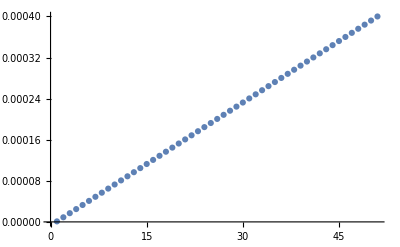

-Graphics-

```mathematica
amin=10^-6;
amax=4 10^-4;
myBins={Table[amin+(amax-amin)*i/50,{i,0,50}]};
ListPlot[myBins]
Histogram[freqsBig,myBins, PlotRange->All]
```

What is the bins if I want about 10 points per bin?  Is that fair to change the binning to do that?  Kelly says that usually astrophysics likes even bins in the Log space.

Binsize 0.0260206 No. bin boundaries 101

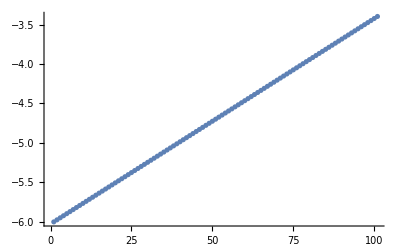

-Graphics-

```mathematica
amin=Log10[1. 10^-6];
amax=Log10[4. 10^-4];
nBins = 100;
myBins={Table[amin+(amax-amin)*i/nBins,{i,0,nBins}]};
Print["Binsize ",(amax-amin)/nBins//N, " No. bin boundaries ", Length[myBins[[1]] ] ]
ListPlot[myBins]
Histogram[Log10[freqsBig],myBins, PlotRange->All,
PlotLabel->"Histogram Log Scale Horizontal",
AxesLabel->{"Log10(freq)","Count"}]
(*Histogram[ Log10[freqsBig]]*)
```

```mathematica
Print["Binsize dLog  ",aa=(amax-amin)/nBins//N, "  10^amin  ", 10^amin//N,"  multiple 10^dLog  ", 10^aa]
```

Binsize dLog  0.0260206  10^amin  1.×10^-6  multiple 10^dLog  1.06175

Binsize 0.130103 No. bin boundaries 21

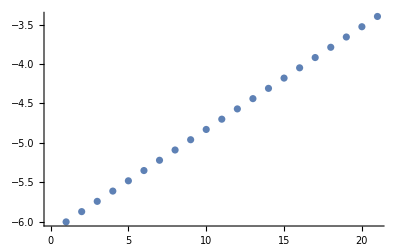

-Graphics-

Binsize dLog  0.130103  10^amin  1.×10^-6  multiple 10^dLog  1.34928

```mathematica
amin=Log10[1. 10^-6];
amax=Log10[4. 10^-4];
nBins = 20;
myBins={Table[amin+(amax-amin)*i/nBins,{i,0,nBins}]};
Print["Binsize ",(amax-amin)/nBins//N, " No. bin boundaries ", Length[myBins[[1]] ] ]
ListPlot[myBins]
Histogram[Log10[freqsBig],myBins, PlotRange->All,
PlotLabel->"Histogram Log Scale Horizontal",
AxesLabel->{"Log10(freq)","Count"}]
(*Histogram[ Log10[freqsBig]]*)
Print["Binsize dLog  ",aa=(amax-amin)/nBins//N, "  10^amin  ", 10^amin//N,"  multiple 10^dLog  ", 10^aa]
```

```mathematica
myBins
(10^#&) /@ myBins
```

{{-6.,-5.8699,-5.73979,-5.60969,-5.47959,-5.34949,-5.21938,-5.08928,-4.95918,-4.82907,-4.69897,-4.56887,-4.43876,-4.30866,-4.17856,-4.04846,-3.91835,-3.78825,-3.65815,-3.52804,-3.39794}}

{{1.×10^-6,1.34928×10^-6,1.82056×10^-6,2.45646×10^-6,3.31445×10^-6,4.47214×10^-6,6.03418×10^-6,8.14181×10^-6,0.0000109856,0.0000148227,0.00002,0.0000269857,0.0000364113,0.0000491291,0.0000662891,0.0000894427,0.000120684,0.000162836,0.000219712,0.000296454,0.0004}}

Find those frequencies in the bin for RMS addition.

```mathematica
Clear[inBin]
inBin[alist_,lower_,upper_] := Module[{aa={}},
For[i=1, i<=Length[alist], i++,
If[alist[[i]]≥lower && alist[[i]]<upper, AppendTo[aa,alist[[i]]], ];
];
aa
]
```

```mathematica
myBins[[1]]
```

{-6.,-5.8699,-5.73979,-5.60969,-5.47959,-5.34949,-5.21938,-5.08928,-4.95918,-4.82907,-4.69897,-4.56887,-4.43876,-4.30866,-4.17856,-4.04846,-3.91835,-3.78825,-3.65815,-3.52804,-3.39794}

```mathematica
Length[myBins[[1]]]
```

21

```mathematica
putInBins = Table[
{aa=inBin[ Log10[freqsBig],myBins[[1]][[ii]],myBins[[1]][[ii+1]]  ],Length[aa]}, {ii,1,Length[myBins[[1]]]-1}
];
```

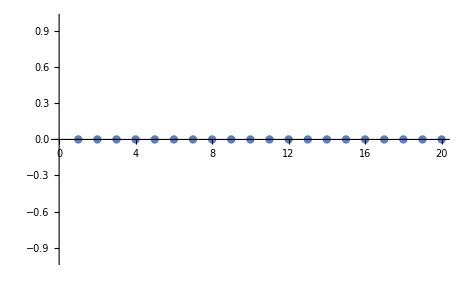

```mathematica
{freqListBin,countBin}=Transpose[putInBins];
ListPlot[countBin]
```

```mathematica
freqListBin[[1;;2]] (* From Exop data, modes in the first bin, second, etc. *)
```

{{},{}}

```mathematica
ListPlot[{freqListBin[[1]], freqListBin[[2]]}, PlotRange->All]
```

-Graphics-

```mathematica
freqsBig[[1;;14]]
```

Part::take: Cannot take positions 1 through 14 in {}.

{}⟦1;;14⟧

```mathematica
{1/freqsBig[[1]], freqsBig[[1]], Log10[freqsBig[[1]]], Floor[  Log10[freqsBig[[1]]] ] }
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1/({}⟦1⟧),{}⟦1⟧,Log[{}⟦1⟧]/Log[10],Floor[Log[{}⟦1⟧]/Log[10]]}

```mathematica
(* Put the bin boundary at the harmonic average of the two points across the boundary. *)
(*findBins[alist_,num_]:=Module[{asort, aa,bb,cc, abins={}},
asort = Sort[alist];
aa=asort[[1]];  (* first point, but bin at next integer down in the mantissa. *)
bb= 10^Floor[  Log10[ aa[[1]]] ]; (* Smallest first, use Log10 and 10 to the power. *)
AppendTo[abins, bb];

bb = Quotient[Length[asort],10]; (* The integer division of the two. *)
aa = Mod[Length[asort],10];  (* The remainder of the division of the two. *)
If[bb==0,
{AppendTo[abins, 10^Ceiling[ Log10[ asort[[-1]] ] ] ],abins},
For[i=1, i≤bb, i++,
AppendTo[abins, Sqrt[ asort[[i*10]]*asort[[i*10+1]] ] ];
],
 ]
*)
```

Exop data from above.
{freqs, hfs}=Transpose[aflat];
Also aflatSort, ordered by frequency,and aflatBig, ordered by frequency and with frequency larger than 1e-6 Hz.

Insert some fake data at 2e-4 Hz and hfs {1,2,3,4,5}e-18 per root hz.  f=2e-4 Hz has not data in that bin!

```mathematica
aflatBig[[1;;4]]
```

Part::take: Cannot take positions 1 through 4 in {}.

{}⟦1;;4⟧

```mathematica
fakeData = {{2. 10^-4,1. 10^-18},{2. 10^-4,2. 10^-18},{2. 10^-4,3. 10^-18},{2. 10^-4,4. 10^-18},{2. 10^-4,5. 10^-18}};
```

```mathematica
If[False,{Length[aflatBig],
aflatBig=aflatBig~Join~fakeData;
Length[aflatBig]}, ] (* Join the fake data to the actual.  Keep this Off most of the time. *)
```

```mathematica
aplot=ListPlot[aflatBig, PlotStyle->{PointSize[0.01]},PlotRange->All]
```

-Graphics-

```mathematica
myBins[[1]]
```

{-6.,-5.8699,-5.73979,-5.60969,-5.47959,-5.34949,-5.21938,-5.08928,-4.95918,-4.82907,-4.69897,-4.56887,-4.43876,-4.30866,-4.17856,-4.04846,-3.91835,-3.78825,-3.65815,-3.52804,-3.39794}

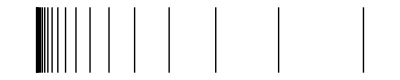

```mathematica
bplot=Show[Graphics[Table[
Line[{{10^(myBins[[1]][[i]]),0.5 10^-18},{10^(myBins[[1]][[i]]),10 10^-18}}],{i,1, Length[myBins[[1]] ]}
]
]
]
```

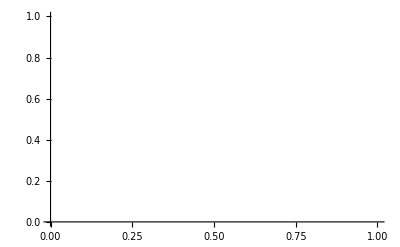

```mathematica
Show[{aplot,bplot}]
```

```mathematica
ListPlot[aflatBig[[1;;50]] ](* first 50 points *)
```

Part::take: Cannot take positions 1 through 50 in {}.

ListPlot::lpn: {}⟦1;;50⟧ is not a list of numbers or pairs of numbers.

ListPlot[{}⟦1;;50⟧]

```mathematica
myBins
```

{{-6.,-5.8699,-5.73979,-5.60969,-5.47959,-5.34949,-5.21938,-5.08928,-4.95918,-4.82907,-4.69897,-4.56887,-4.43876,-4.30866,-4.17856,-4.04846,-3.91835,-3.78825,-3.65815,-3.52804,-3.39794}}

Bin the aflatBig.  2D version of BinLists looks like the right way to go.  The second dimension is {{-Infinity,Infinity}} for the binning, this also adds an extra set of parentheses.

```mathematica
(* use myBins, in the log-space of freqency from 1e-6 to 4e-4 Hz *)

pairsInBin={};
{freqBig, hfsBig}=Transpose[aflatBig];
aflatBigLogFreq = Transpose[ {Log10[freqBig],hfsBig}];
aflatBL=BinLists[aflatBigLogFreq,myBins,{{-∞,+∞}}];
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Set::shape: Lists {freqBig,hfsBig} and Transpose[{}] are not the same shape.

Transpose::nmtx: The first two levels of {Log[freqBig]/Log[10],hfsBig} cannot be transposed.

BinLists::vectmat: The first argument is expected to be a vector or matrix.

```mathematica
{aflatBigLogFreq[[-7;;-1]],hfsBig[[-7;;-1]]}
```

Part::take: Cannot take positions -7 through -1 in Transpose[{Log[freqBig]/Log[10],hfsBig}].

Part::take: Cannot take positions -7 through -1 in hfsBig.

{Transpose[{Log[freqBig]/Log[10],hfsBig}]⟦-7;;-1⟧,hfsBig⟦-7;;-1⟧}

```mathematica
10^-1.6987
```

0.0200124

```mathematica
aflatBL[[-3;;-1]]
```

BinLists[Transpose[{Log[freqBig]/Log[10],hfsBig}],{{-6.,-5.8699,-5.73979,-5.60969,-5.47959,-5.34949,-5.21938,-5.08928,-4.95918,-4.82907,-4.69897,-4.56887,-4.43876,-4.30866,-4.17856,-4.04846,-3.91835,-3.78825,-3.65815,-3.52804,-3.39794}},{{-∞,∞}}]

```mathematica
{Length[aflatBig], Length[myBins],Length[aflatBL], Length[aflatBL[[1,1]]],Length[aflatBL[[2,1]]]}
aflatBL[[-1,1]]
(*Transpose[  aflatBL[[8,1]]  ]
aflatBL[[8,1]]*)
```

{0,1,3,2,21}

{-∞,∞}

```mathematica
(* Check the count, all elements of the bin lists should equal the original vector length. *)
(* Woo Hoo! Length[aflatBig] == sum of the lengths of the binned vector! *)
```

```mathematica
Sum[Length[aflatBL[[i,1]] ],{i,1,Length[aflatBL]}]
```

25

```mathematica
{Length[myBins], Length[myBins[[1]]], (myBins[[1,2]]-myBins[[1,1]]),(myBins[[1,3]]-myBins[[1,2]]), 10^ (myBins[[1,3]]-myBins[[1,2]])}
```

{1,21,0.130103,0.130103,1.34928}

```mathematica
Clear[addLikeRMS];
addLikeRMS[a_]:=Sqrt[ Sum[a[[i]]^2,{i,1,Length[a]} ] ]
```

```mathematica
??addLikeRMS
```

Global`addLikeRMS

addLikeRMS[a_]:=√(∑_(i=1)^Length[a] a⟦i⟧^2)

```mathematica
{ addLikeRMS[{1. 10^-18,2. 10^-18,3. 10^-18,4. 10^-18,5. 10^-18}], Sqrt[ 1*1+2*2+3*3+4*4+5*5 ]//N}
```

{7.4162×10^-18,7.4162}

```mathematica
(* Add up within the bin the hfs like RMS. Use the CENTROID of the log-space frequency??!!   *)
logfreq={};
hfsrms={};
cntLogfreq={};
cntHfsrms = {};
For[i=1,i≤Length[aflatBL],i++,
If[ Length[ aflatBL[[i,1]] ]≠0,
Module[{alogFreq={},aHfs={} },
(*Print["  i is ",i];*)
{alogFreq, aHfs}=Transpose[ aflatBL[[i,1]] ];
logfreq~AppendTo~( Mean[ alogFreq ] ); (*( (myBins[[1,i]]+myBins[[1,i+1]])/2 );*)
If[i==12,Print["aHfs and addLikeRMS\n",aHfs, "\n",addLikeRMS[aHfs] ];, ];
hfsrms~AppendTo~addLikeRMS[ aHfs ]; 
cntLogfreq~AppendTo~Length[alogFreq];
cntHfsrms~AppendTo~Length[ aHfs ];
],
{
(*Print["*** Zero length aflatBL, i is ",i];*)
logfreq~AppendTo~( Mean[ {myBins[[1,i]], myBins[[1,i+1]]} ] );
hfsrms~AppendTo~( 0.0 );
cntLogfreq~AppendTo~(0);
cntHfsrms~AppendTo~(0);
}
]
]
```

Transpose::nmtx: The first two levels of {Log[freqBig]/Log[10],hfsBig} cannot be transposed.

Set::shape: Lists {alogFreq$114464,aHfs$114464} and Transpose[{Log[freqBig]/Log[10],hfsBig}] are not the same shape.

Transpose::nmtx: The first two levels of {-6.,-5.8699,-5.73979,-5.60969,-5.47959,-5.34949,«9»,-4.04846,-3.91835,-3.78825,-3.65815,-3.52804,-3.39794} cannot be transposed.

Set::shape: Lists {alogFreq$114469,aHfs$114469} and Transpose[{-6.,-5.8699,-5.73979,-5.60969,-5.47959,-5.34949,«9»,-4.04846,-3.91835,-3.78825,-3.65815,-3.52804,-3.39794}] are not the same shape.

Transpose::nmtx: The first two levels of {-∞,∞} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Set::shape: Lists {alogFreq$114474,aHfs$114474} and Transpose[{-∞,∞}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

-Graphics-

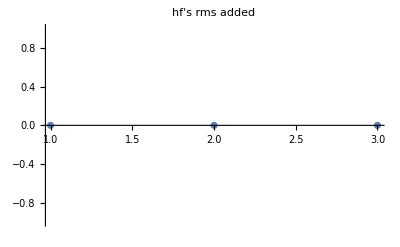

```mathematica
ListPlot[logfreq, PlotLabel->"Log Freq"]
ListPlot[hfsrms, PlotLabel->"hf's rms added", PlotRange->All]
```

Convert into data like the other hf’s in the Grace plots...just pairs of freq and hfs to export.

```mathematica
rmsHfData=Transpose[  {10^logfreq, hfsrms} ];
```

```mathematica
rmsHfData
```

{{10^Mean[{}],0},{10^Mean[{}],0},{10^Mean[{}],0}}

```mathematica
{{"Freq","hfs RMS sum"}}~Join~rmsHfData//TableForm
```

Freq | hfs RMS sum
10^Mean[{}] | 0
10^Mean[{}] | 0
10^Mean[{}] | 0

```mathematica
ListPlot[rmsHfData]
```

-Graphics-

```mathematica
Export[myDir<>"hfsRMS20bins.dat",rmsHfData ]
```

/home/gabella/Documents/astro/exop/hfsRMS20bins.dat

Put in some fake data to check the RMS addition.  At 2e-2 Hz and at values 1,2,3,4,5 e -18 per root Hz.

## Possible LISA bandwidths for root-mean-squaring of the GW modes in freq space.

one year, three year, one day, one hour

```mathematica
{1/(3.1 10^7), 1/(3.*3.1 10^7), 1/(24.*3600.),1/(3600.), Sqrt[3.1 10^7], 1/Sqrt[3.1 10^7]}
```

{3.22581×10^-8,1.07527×10^-8,0.0000115741,0.000277778,5567.76,0.000179605}

LISA Arm lengths and the ripples on the right of the sensitivity curve.  TOF?

```mathematica
Clear[tof];
tof[arm_,n_]:= n*2*arm/cee
```

```mathematica
{{"n","time, 5e9", "freq, 1e9", "time, 5e9", "freq, 1e9"}}~Join~Table[{n, aa=tof[5 10^9,n],1/aa, bb=tof[1 10^9,n], 1/bb},{n,1,5}]//TableForm
```

n | time, 5e9 | freq, 1e9 | time, 5e9 | freq, 1e9
1 | 33.3564 | 0.0299792 | 6.67128 | 0.149896
2 | 66.7128 | 0.0149896 | 13.3426 | 0.0749481
3 | 100.069 | 0.00999308 | 20.0138 | 0.0499654
4 | 133.426 | 0.00749481 | 26.6851 | 0.0374741
5 | 166.782 | 0.00599585 | 33.3564 | 0.0299792

Tinto et al. 2002, page 38,  say BW 1cycle per year or 3.17e-8 Hz (?).

## BarCharts make me crazy; why so hard to see the x values and so far only with PlotTheme->Web, and a few other themes, and explicitly at the end of a Show[].

```mathematica
p=Table[{n^1.3,Prime[n]},{n,10}]
```

{{1.,2},{2.46229,3},{4.17117,5},{6.06287,7},{8.10328,11},{10.2706,13},{12.5495,17},{14.9285,19},{17.3986,23},{19.9526,29}}

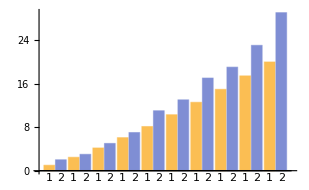

```mathematica
BarChart[p, ChartLabels->Range[10]]
```

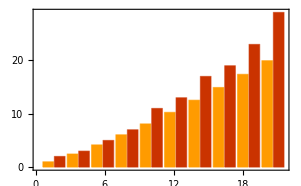

```mathematica
BarChart[p,PlotTheme->"Web"]
```

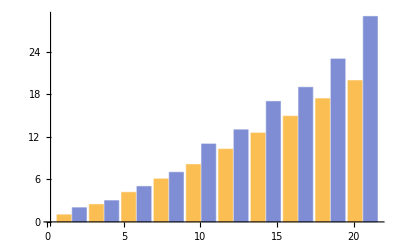

```mathematica
Show[ BarChart[p, Axes->None],Axes->True, Ticks->Automatic] (* Weird! *)
```